# Input data

```mathematica
FNVHash[data_,old_]:=Module[{prime,hash},
prime=1099511628211;
hash=old;
Do[hash=Mod[BitXor[hash,block]*prime,2^64],{block,data}];
hash
]

DoubleToByte[a_]:=ImportString[ExportString[{a},"Real64"],"Byte"];
IntToByte[a_]:=ImportString[ExportString[{a},"Integer32"],"Byte"];

IdFermionLadder[L_,D_,Jl_,Jr_,Δl_,Δr_,h_,γ_,μL1_,μL2_,μR1_,μR2_,ΓL1_,ΓL2_,ΓR1_,ΓR2_]:=Module[{hash},
hash=14695981039346656037;

hash=FNVHash[IntToByte[L],hash];
hash=FNVHash[IntToByte[D],hash];
hash=FNVHash[DoubleToByte[Jl],hash];
hash=FNVHash[DoubleToByte[Jr],hash];
hash=FNVHash[DoubleToByte[Δl],hash];
hash=FNVHash[DoubleToByte[Δr],hash];
hash=FNVHash[DoubleToByte[h],hash];
hash=FNVHash[DoubleToByte[γ],hash];
hash=FNVHash[DoubleToByte[μL1],hash];
hash=FNVHash[DoubleToByte[μL2],hash];
hash=FNVHash[DoubleToByte[μR1],hash];
hash=FNVHash[DoubleToByte[μR2],hash];
hash=FNVHash[DoubleToByte[ΓL1],hash];
hash=FNVHash[DoubleToByte[ΓL2],hash];
hash=FNVHash[DoubleToByte[ΓR1],hash];
hash=FNVHash[DoubleToByte[ΓR2],hash];

hash
]

FermionLadderData[L_,D_,Jl_,Jr_,Δl_,Δr_,h_,γ_,μL1_,μL2_,μR1_,μR2_,ΓL1_,ΓL2_,ΓR1_,ΓR2_]:=Module[{ID,monitor,Jctrl,Bond,Mup,Mdown,Corrup,Corrdown,Jup,Jdown,Jrung,Spec,χ},
SetDirectory[NotebookDirectory[]];
ID=IdFermionLadder[L,D,Jl,Jr,Δl,Δr,h,γ,μL1,μL2,μR1,μR2,ΓL1,ΓL2,ΓR1,ΓR2];

monitor=BinaryReadList["output/open/Monitor_"<>ToString[ID]<>".bin", {"Real64","Real64","Real64"}];
Mup=BinaryReadList["output/open/Mup_"<>ToString[ID]<>".bin", "Real64"];
Mdown=BinaryReadList["output/open/Mdown_"<>ToString[ID]<>".bin", "Real64"];
Corrup=BinaryReadList["output/open/Corrup_"<>ToString[ID]<>".bin", "Real64"];
Corrdown=BinaryReadList["output/open/Corrdown_"<>ToString[ID]<>".bin", "Real64"];
Jup=BinaryReadList["output/open/Jup_"<>ToString[ID]<>".bin", "Real64"];
Jdown=BinaryReadList["output/open/Jdown_"<>ToString[ID]<>".bin", "Real64"];
Jrung=BinaryReadList["output/open/Jrung_"<>ToString[ID]<>".bin", "Real64"];
Spec=BinaryReadList["output/open/Spectrum_"<>ToString[ID]<>".bin", "Real64"];
χ=BinaryReadList["output/open/Cov_"<>ToString[ID]<>".bin", {"Real64","Real64"}];

Jctrl={monitorᵀ[[1]],monitorᵀ[[2]]}ᵀ;
Bond={monitorᵀ[[1]],monitorᵀ[[3]]}ᵀ;
Corrup=ArrayReshape[Corrup,{L,L}];
Corrdown=ArrayReshape[Corrdown,{L,L}];
χ=Table[χ[[i,1]]+I χ[[i,2]],{i,Length[χ]}];
χ=ArrayReshape[χ,{2L,2L}];

Mup=Table[{(i-1)/(L-1),(Mup[[i]]+1)/2},{i,L}];
Mdown=Table[{(i-1)/(L-1),(Mdown[[i]]+1)/2},{i,L}];
Jup=Table[{i,Jup[[i]]},{i,L-1}];
Jdown=Table[{i,Jdown[[i]]},{i,L-1}];
Jrung=Table[{i,Jrung[[i]]},{i,L}];

{Jctrl,Bond,Mup,Mdown,Jup,Jdown,Jrung,Spec,Corrup,Corrdown,χ}
]

FermionPlots[L_,D_,Jl_,Jr_,Δl_,Δr_,h_,γ_,μL1_,μL2_,μR1_,μR2_,ΓL1_,ΓL2_,ΓR1_,ΓR2_]:=Module[{data,plots,Legends},
plots={};
data=FermionLadderData[L,D,Jl,Jr,Δl,Δr,h,γ,μL1,μL2,μR1,μR2,ΓL1,ΓL2,ΓR1,ΓR2];

AppendTo[plots,ListLinePlot[data[[1]],PlotRange->All,AxesLabel->{"t","J_t"},PlotLabel->"Current over time"]];
AppendTo[plots,ListLogLinearPlot[data[[2]],Joined->True,AxesLabel->{"t","Bond"}]];
AppendTo[plots,ListLogPlot[data[[8]],AxesLabel->{"i","σ"},Joined->True,PlotLabel->"Singular Values"]];
AppendTo[plots,ListLinePlot[data[[3]],AxesLabel->{"(i-1)/(L-1)","n_up"},PlotLabel->"Occupation Upper Chain"]];
AppendTo[plots,ListLinePlot[data[[4]],AxesLabel->{"(i-1)/(L-1)","n_down"},PlotLabel->"Occupation Lower Chain"]];
AppendTo[plots,ListLinePlot[data[[5]],AxesLabel->{"i","J_up"},PlotLabel->"Current Upper Chain"]];
AppendTo[plots,ListLinePlot[data[[6]],AxesLabel->{"i","J_down"},PlotLabel->"Current Lower Chain"]];
AppendTo[plots,ListLinePlot[data[[7]],AxesLabel->{"i","J_rung"},PlotLabel->"Current Rung"]];

AppendTo[plots,MatrixPlot[data[[9]],AxesLabel->{"x","y"},PlotLabel->"Correlation <n_up n_up>",PlotLegends->True]];
AppendTo[plots,MatrixPlot[data[[10]],AxesLabel->{"x","y"},PlotLabel->"Correlation <n_down n_down>",PlotLegends->True]];
AppendTo[plots,MatrixPlot[data[[-1]]//Re,AxesLabel->{"x","y"},PlotLabel->"Real part of SPA",PlotLegends->True]];
AppendTo[plots,MatrixPlot[data[[-1]]//Im,AxesLabel->{"x","y"},PlotLabel->"Imaginary part of SPA",PlotLegends->True]];

ArrayReshape[plots,{2,6}]
]
```

# Results

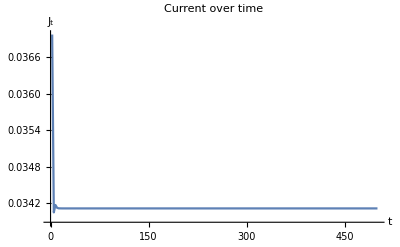
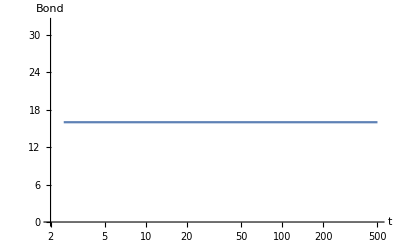
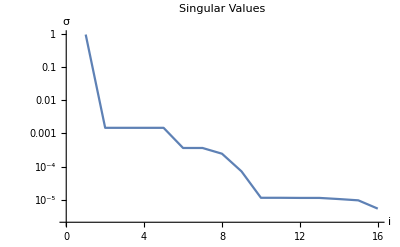
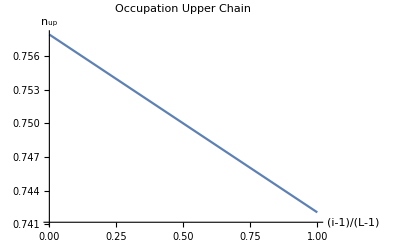
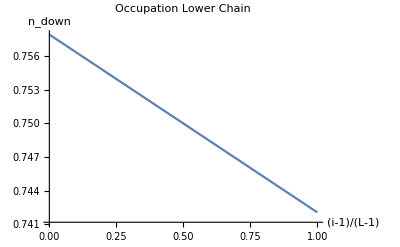
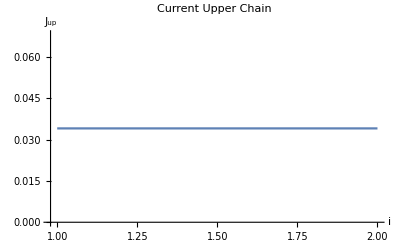
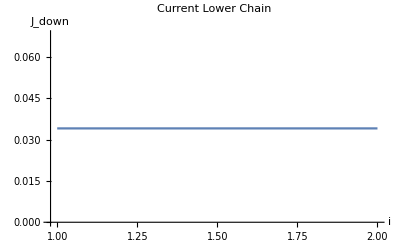
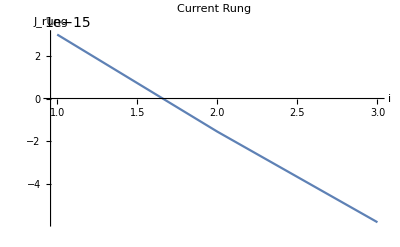
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
FermionPlots[3,16,-1.0,-1.0,1.5,1.5,0.0,0.0,0.1,0.1,0.1,0.1,1.0,1.0,1.0,1.0]
```